## Phase space for damped pendulum

```mathematica
(* set damping factor *)
```

```mathematica
b:=0.2;
```

```mathematica
(* values A,B are the initial conditions for our trajectory *)
```

```mathematica
Clear[soln]
soln[A_,B_]:=Module[{tmp},
NDSolve[{θ''[t]==-Sin[θ[t]]-b*θ'[t],θ[0]==A,θ'[0]==B},θ,{t,0,25}][[1]]
]
```

```mathematica
soln[1,0]
θ[1]/.%
```

{θ→InterpolatingFunction[{{0., 25.}}, <>]}

0.625123

```mathematica
(* Plot the fixed points *)
```

{{-12.5664,0.},{-9.42478,0.},{-6.28319,0.},{-3.14159,0.},{0.,0.},{3.14159,0.},{6.28319,0.},{9.42478,0.},{12.5664,0.}}

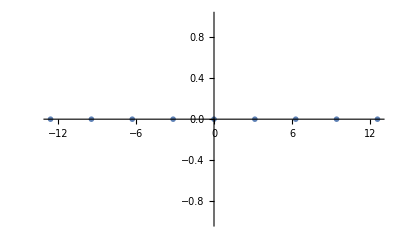

{{1.,1.},{-1.,1.},{1.,1.},{-1.,1.},{1.,1.},{-1.,1.},{1.,1.},{-1.,1.},{1.,1.}}

```mathematica
Table[{π*n,0},{n,-4,4,1}]//N
pltFPts=ListPlot[%,PlotMarkers->{Automatic,Medium}]
Cos[%%]
```

```mathematica
(* Plot trajectories *)
```

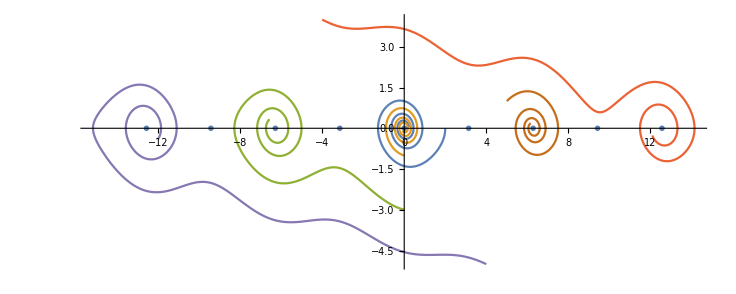

```mathematica
Show[
ParametricPlot[Evaluate[{
{θ[t],θ'[t]}/.soln[2,0],
{θ[t],θ'[t]}/.soln[0,-1],
{θ[t],θ'[t]}/.soln[0,-3],
{θ[t],θ'[t]}/.soln[-4,4],
{θ[t],θ'[t]}/.soln[4,-5],
{θ[t],θ'[t]}/.soln[5,1]
}],{t,0,20},PlotRange->All],pltFPts
]
```

```mathematica
(* Plot more trajectories *)
```

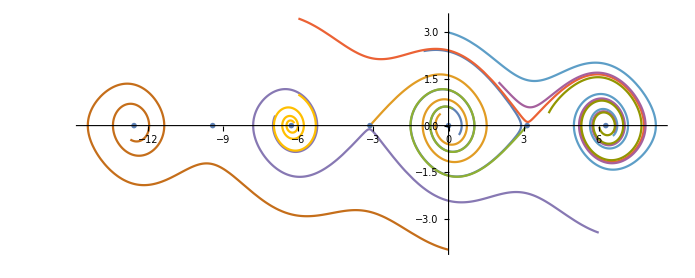

```mathematica
Show[
ParametricPlot[Evaluate[{
{θ[t],θ'[t]}/.soln[-1,2.4],
{θ[t],θ'[t]}/.soln[-3.13,0],
{θ[t],θ'[t]}/.soln[3.14,0],
{θ[t],θ'[t]}/.soln[-6,3.45],
{θ[t],θ'[t]}/.soln[6,-3.45],
{θ[t],θ'[t]}/.soln[0,-4],
{θ[t],θ'[t]}/.soln[0,3],
{θ[t],θ'[t]}/.soln[-6,1],
{θ[t],θ'[t]}/.soln[2,1.4],
{θ[t],θ'[t]}/.soln[4,.4]
}],{t,0,20},PlotRange->All]
,pltFPts]
```